```mathematica
SetDirectory[NotebookDirectory[]];
```

## 正方点阵

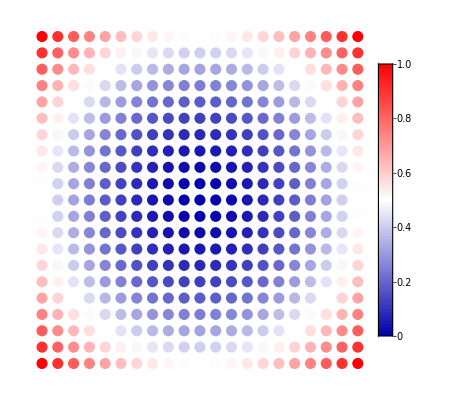

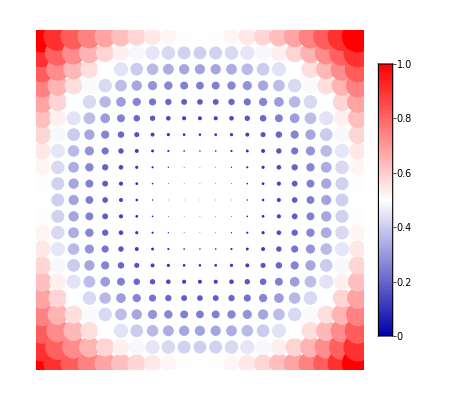

```mathematica
dx=1;
zColor=Flatten[Table[i/10,{i,0,10,dx}],1];
b2=BarLegend[{Blend[{Darker@Blue,White,Red},#]&/@zColor,MinMax[zColor]},LegendMarkerSize->200,LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Bold}];
p1=Graphics[{ParallelTable[{Blend[{Darker@Blue,White,Red},(x^2+y^2)/200],PointSize[0.02],EdgeForm[{Thick,Black}],Point[RotationMatrix[0 Degree].{x,y}]},{x,-10,10,dx},{y,-10,10,dx}],Inset[b2,{15,0},Center,10]}]
p2=Graphics[{ParallelTable[{Blend[{Darker@Blue,White,Red},(x^2+y^2)/200],PointSize[(x^2+y^2)/3500],EdgeForm[{Thick,Black}],Point[RotationMatrix[0 Degree].{x,y}]},{x,-10,10,dx},{y,-10,10,dx}],Inset[b2,{15,0},Center,10]}]
Export["den1.png",p1,ImageScaled->1200,ImageResolution->200];
Export["den2.png",p2,ImageScaled->1200,ImageResolution->200];
```

```mathematica
dx=2;
zColor=Flatten[Table[i/10,{i,0,10,dx}],1];
b2=BarLegend[{Blend[{Darker@Blue,White,Red},#]&/@zColor,MinMax[zColor]},LegendMarkerSize->250,LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black}];
p1=Graphics3D[{ParallelTable[{Blend[{Blue,White,Red},(x^2+y^2+z^2)/300],PointSize[0.02],EdgeForm[{Thick,Black}],Point[RotationMatrix[0 Degree,{0,0,1}].{x,y,z}]},{x,-10,10,dx},{y,-10,10,dx},{z,-10,10,dx}],Inset[b2,{20,-10,0},Right,80]},Boxed->False]
p2=Graphics3D[{ParallelTable[{Blend[{Darker@Blue,White,Red},(x^2+y^2+z^2)/300],PointSize[(x^2+y^2)/3500],EdgeForm[{Thick,Black}],Point[RotationMatrix[0 Degree,{0,0,1}].{x,y,z}]},{x,-10,10,dx},{y,-10,10,dx},{z,-10,10,dx}],Inset[b2,{20,-10,0},Right,80]},Boxed->False]
Export["den3.png",p1,ImageScaled->1200,ImageResolution->200];
Export["den4.png",p2,ImageScaled->1200,ImageResolution->200];
```

-Graphics3D-

-Graphics3D-

## 六角点阵

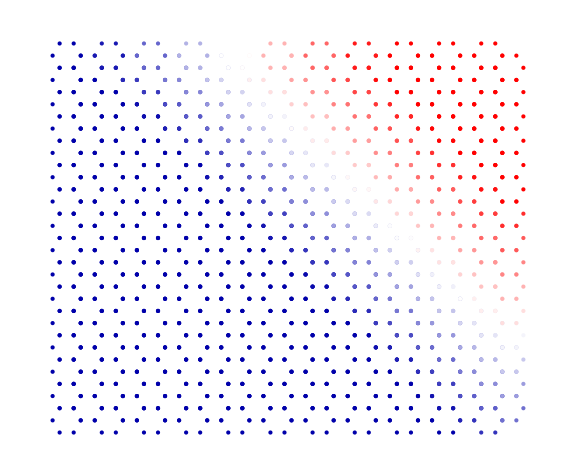

```mathematica
g[x_,y_]:=Point[Table[{Cos[2Pi k/6]+x,Sin[2Pi k/6]+y},{k,6}]]
dx=0.1;
len=20;
g[x_,y_]:=Table[{Blend[{Darker@Blue,White,Red},(x+y)/len],Point[{Cos[2Pi k/6]+x,Sin[2Pi k/6]+y}]},{k,6}]
layer1=Graphics[{PointSize[Large],EdgeForm[Black],Lighter@Lighter@Blue,Table[g[3i+3((-1)^j+1)/4,Sqrt[3]/2j],{i,-5,5},{j,-15,15}]},ImageSize->Large]
```

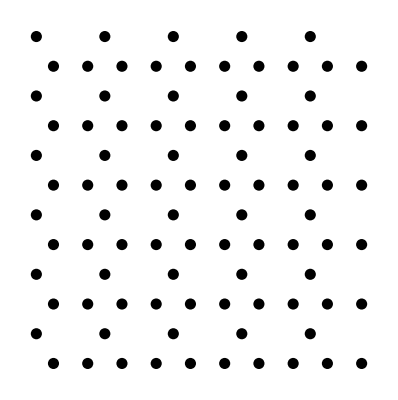

```mathematica
ax=1.0;
ay=2ax;
xlen=10;
ylen=xlen+1;
posX[x_]:=Table[{i0,(√3)/2 x},{i0,1,xlen,ax}];
posY[y_]:=Table[{i0-ax/2,(√3)/2*y},{i0,1,xlen,ay}];
points=Flatten[Join[Table[posX[i],{i,0,xlen,2}],Table[posY[i],{i,1,ylen,2}]],1];
Graphics[{PointSize[0.02],Point[points]}]
```

## 三角点阵

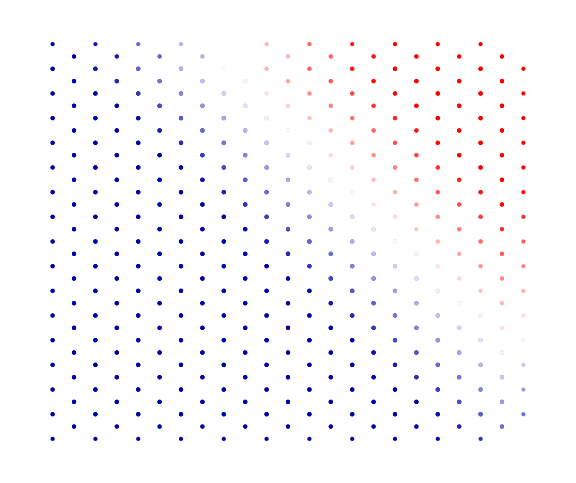

```mathematica
g[x_,y_,n_]:=Point[Table[{Cos[2Pi k/n]+x,Sin[2Pi k/n]+y},{k,n}]]
dx=0.1;
len=20;
g[x_,y_,n_]:=Table[{Blend[{Darker@Blue,White,Red},(x+y)/len],Point[{Cos[2Pi k/n]+x,Sin[2Pi k/n]+y}]},{k,n}]
layer1=Graphics[{PointSize[Large],EdgeForm[Black],Lighter@Lighter@Blue,Table[g[3i+3((-1)^j+1)/4,Sqrt[3]/2j,3],{i,-5,5},{j,-15,15}]},ImageSize->Large]
```